## Models

```mathematica
Import[NotebookDirectory[]<>"ExplicitThinPlateElasticitylib.m"];
```

All elements are in good condition

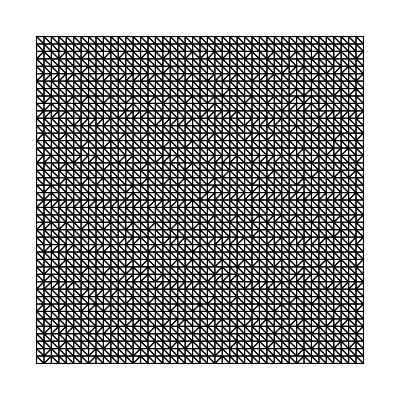

```mathematica
L=0.5;H=0.5;thickness0=0.01;udim=1;ndim=2;dx=L/40;
coord=N[GridNdim[{0,0}-2dx,{L, H}+2dx,dx]];
Nnode=Length[coord];
ndof=Nnode udim;
uvw=ConstantArray[0.,{Nnode,udim}];
pvol=L*H/Nnode;
nExt=10orderDeri;
numNei=numDeri+nExt;
numNei=20;
Nei=nearestNeighbours[coord,numNei];
pvol=ConstantArray[pvol,Nnode];
mesh1=MyDelaunayMesh[coord];
ShowMesh[mesh1]
```

```mathematica
WeiF=QuinticKer;(*WeiF[r_,h_]:=1;*)WeiF=Wfr2;
np=-1;
hgPen=1.0;
{PW,KHG}=NOMPwKhg[np,coord,pvol,Nei,pfun,WeiF,hgPen ];
```

For selected nodes:{1493,1162,1178,1713,471,1272,817,2014,1748,285}

Condition number of NOM:{5.95238,5.95238,5.95238,5.95238,5.95238,5.95238,5.95238,39.3115,5.95238,5.95238}

```mathematica
forceList=FindPoints[coord,{0,0}+0.1dx,{L,L}-0.1 dx];
fixList=Complement[Range[Nnode],forceList];
hgList=Complement[Range[Nnode],FindPoints[coord,{0,0}+2dx,{L,L}-2dx]];
```

```mathematica
pDirichlet=10.^6;
fixFun[xyz_List]:=ConstantArray[0.,udim];
fx=10.^6;forceFun[xyz_List]:={fx dx^2};
fixValues=BCValuesFunc[fixList,coord,fixFun,udim];
forceValues=BCValuesFunc[forceList,coord,forceFun,udim];
dofFix=DofIndexValue[fixList,fixValues];
dofForce=DofIndexValue[forceList,forceValues];
```

```mathematica
dofVelo={{},{}};
```

```mathematica
rindex=ParticleNeighDof[Nei,udim];
```

```mathematica
AbortOnMessage[]
```

```mathematica
phg0
```

1.74565×10^13

```mathematica
El0
```

3.×10^10

```mathematica
phg0/El0
```

0.0581885

```mathematica
El0=210. 10^9;nu0=0.3;thickness0=thickness0;rho0=7850.;phg0=0El0;
massMatrix=Flatten[Table[ConstantArray[thickness0 rho0 pvol[[i]],udim],{i,Length[pvol]}]];
veloSound=Sqrt[El0/rho0];tIncMax=dx/veloSound;
ctime=0.;
tInc=0.4tIncMax;
TotalTime=10 tInc;
phg0List=ConstantArray[phg0,{Nnode}];
phg0List[[hgList]]=400 El0;
```

```mathematica
phg0List//Dimensions
```

{2025}

```mathematica
udof=ConstantArray[0.,{ndof}];
vdof=ConstantArray[0.,{ndof}];
adof=ConstantArray[0.,{ndof}];
adofNew=adof;
```

```mathematica
weiNeiList=WeiNeiList[coord,WeiF,Nei];
```

```mathematica
umaxList={};
vmaxList={};
amaxList={};
```

```mathematica
pcenter=FindPoints[coord,{L,L}0.5-0.2dx,{L,L}0.5+0.2dx][[1]]
```

1013

```mathematica
internalF//Max
```

internalF

```mathematica
vdof//Max
```

6055.5

```mathematica
SaveStepList={1000,1500,2000,2500,3000};
```

```mathematica
outputInterval=400;j=1;
Do[udof+=tInc vdof+(0.5 tInc^2)adof;
udof[[dofFix[[1]]]]=dofFix[[2]];(*displacement constraint*)
AppendTo[umaxList,{ctime,udof[[pcenter]]}];
AppendTo[vmaxList,{ctime,vdof[[pcenter]]}];
AppendTo[amaxList,{ctime,adof[[pcenter]]}];
uvw=ArrayReshape[udof,{Nnode,udim}];
(*deriU=NOMPartialU0[uvw,PW,Nei];*)
(*deformList=FList[coord,coord0,NeiList,invKList,vol,WeiF];*)
(*internalF=ForceList[bulkK,shearG,coord,coord0,NeiList,deformList,invKList,trKList,WeiF,vol,penCoef];*)
internalF=-NOMResiPreValue3[Resi1,ndim,pvol,{El0,nu0,thickness0},uvw,PW,KHG,weiNeiList,Nei,rindex,phg0List];(*-NOMResiPreValue2[Resi1,ndim,pvol,{El0,nu0,phg0},uvw,PW,KHG,Nei,rindex,phg0];*)
internalF-=0.4vdof;
internalF[[dofForce[[1]]]]+=dofForce[[2]];(*add boundary forces to the internal force vector*)
adofNew=internalF/massMatrix;
vdof+=0.5 tInc (adof+adofNew);
If[MemberQ[SaveStepList,j],SaveToCell[{udof,vdof},"time:"<>ToString[ctime]]];
vdof[[dofVelo[[1]]]]=dofVelo[[2]];(*velocity constraint*)
adof=adofNew;
If[Mod[j,outputInterval]==1,Print["acc max:",Max[adofNew],",vel max:",Max[vdof],",umax: ",Max[udof]];
Print["step=",j,",t=",ctime," done"];];
ctime+=tInc;j++;
If[Mod[j,outputInterval]==1,Print[Plot2DField[uvw[[All,1]],mesh1]];(*Print[Plot2DField[uvw[[All,2]],mesh1]]*)]
,{i,4000}]
```

```mathematica
{udof1,vdof1}="time:0.00676599";
```

```mathematica
{udof2,vdof2}="time:0.00628263";
```

```mathematica
{udof3,vdof3}="time:0.00579928";
```

```mathematica
{udof4,vdof4}="time:0.00531593";
```

```mathematica
{udof5,vdof5}="time:0.00483257";
```

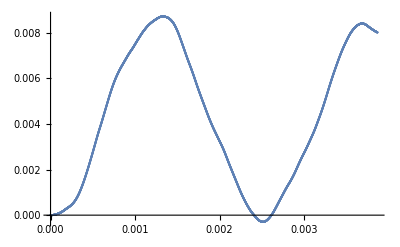

```mathematica
ListPlot[umaxList]
```

```mathematica
SaveToCell[coord,"clamped coordinate"]
```

```mathematica
coord="clamped coordinate";
```

```mathematica
{4.83257,5.31159,5.799,6.283,6.766}-3.86683
```

{0.96574,1.44476,1.93217,2.41617,2.89917}

```mathematica
dx/=1.1;
```

```mathematica
MyPlotPoint[coord,udof1]
MyPlotPoint[coord,udof2]
MyPlotPoint[coord,udof3]
MyPlotPoint[coord,udof4]
MyPlotPoint[coord,udof5]
```

-Graphics3D-

{Null}

-Graphics3D-

{Null}

-Graphics3D-

{Null}

-Graphics3D-

{Null}

-Graphics3D-

{Null}

```mathematica
SaveToCell[{umaxList,vmaxList}]
```

```mathematica
{umaxList,vmaxList}="data";
```